```mathematica
datastring=Import[NotebookDirectory[]<>"opvalues_nodeg.txt"];
```

```mathematica
header = ImportString[datastring,"Table"][[1;;2]];data=Drop[ImportString[datastring,"Table"],2];
```

```mathematica
header
```

{{#,L=,53,beta=,100.,t_max=,15.,steps=,1500,D=,50,#},{t,E,mag}}

```mathematica
data//Dimensions
```

{150,44}

```mathematica
3+13+2*13
```

42

```mathematica
3+13+2+13+13
```

44

```mathematica
szsz[r_]:=data[[All,4+r]];
sz[m_]:=data[[All,3+13+2+m]];
con[tk_,r_]:=((szsz[r]-sz[13+r]sz[13-r])/szsz[r])[[tk]];
```

```mathematica
szsz[12]
```

{0.993857,0.977756,0.95746,0.939912,0.930611,0.931831,0.942094,0.956891,0.970396,0.977624,0.976222,0.967084,0.953594,0.939978,0.929634,0.924125,0.923072,0.924791,0.927263,0.928999,0.929437,0.928781,0.927481,0.925714,0.923186,0.919346,0.913874,0.907114,0.900168,0.894549,0.891521,0.891463,0.893537,0.895879,0.89626,0.893001,0.885713,0.875526,0.864684,0.855677,0.850332,0.849195,0.851424,0.855192,0.858418,0.859542,0.858038,0.854456,0.850029,0.846061,0.843393,0.842142,0.841791,0.84152,0.840615,0.838774,0.836172,0.833322,0.830805,0.82903,0.828114,0.827919,0.828182,0.828672,0.829274,0.829984,0.830833,0.831802,0.832785,0.833616,0.834148,0.834337,0.834263,0.834096,0.834006,0.834078,0.834266,0.83443,0.834418,0.834158,0.833711,0.833252,0.832987,0.833048,0.833418,0.833924,0.834306,0.834326,0.83387,0.832996,0.831911,0.830887,0.830153,0.829825,0.829878,0.83019,0.830604,0.831,0.831325,0.831588,0.831823,0.832049,0.832243,0.83235,0.832312,0.832101,0.831736,0.831278,0.830807,0.830392,0.830069,0.829845,0.829713,0.829668,0.82972,0.829885,0.830164,0.830529,0.830917,0.831243,0.83143,0.831444,0.831308,0.831094,0.830899,0.8308,0.830832,0.830972,0.831161,0.831328,0.831428,0.831454,0.831434,0.83141,0.831409,0.831431,0.831441,0.831389,0.831235,0.830969,0.830615,0.830226,0.829862,0.829574,0.82939,0.829314,0.829336,0.829443,0.829622,0.829859,0.830137,0.83043,0.830704,0.830923,0.831062,0.831115,0.831099,0.831043,0.83098,0.830926,0.830884,0.830847,0.830808,0.830766,0.830731,0.830726,0.830772,0.830875,0.831013,0.831147,0.831237,0.831256,0.831192,0.831051,0.830871,0.830707,0.83061,0.830602,0.830675,0.830802,0.830962,0.831154,0.831377,0.831617,0.831841,0.832014,0.832129,0.832197,0.832219,0.832176,0.832058,0.831886,0.831708,0.831563,0.831463,0.831398,0.831357,0.831346,0.831377,0.83146}

```mathematica
data[[1,4;;17]]
```

{8.22689×10^-7,0.994552,0.994552,0.994552,0.994552,0.994552,0.994552,0.994551,0.994551,0.994551,0.994551,0.994551,0.994551,0.994427}

```mathematica
sz[13]
```

{-0.996924,-0.988815,-0.978499,-0.96949,-0.964682,-0.965314,-0.970616,-0.978213,-0.985105,-0.988801,-0.98817,-0.983691,-0.977083,-0.970517,-0.965759,-0.963614,-0.963806,-0.965314,-0.966918,-0.967716,-0.967395,-0.966182,-0.964574,-0.963007,-0.961642,-0.960351,-0.958875,-0.957042,-0.954915,-0.952794,-0.95107,-0.950026,-0.949681,-0.949771,-0.949859,-0.949525,-0.948542,-0.94695,-0.945005,-0.943041,-0.941317,-0.939924,-0.938786,-0.937746,-0.936673,-0.935538,-0.934416,-0.933416,-0.9326,-0.931921,-0.931229,-0.930338,-0.92912,-0.927574,-0.92583,-0.924101,-0.922582,-0.921375,-0.920455,-0.919692,-0.918929,-0.918049,-0.917022,-0.915895,-0.914745,-0.913626,-0.912531,-0.911405,-0.910182,-0.908837,-0.907411,-0.906006,-0.904735,-0.903671,-0.902807,-0.902056,-0.901289,-0.900393,-0.899314,-0.898076,-0.896757,-0.895448,-0.894209,-0.893047,-0.891928,-0.890807,-0.889664,-0.888516,-0.887409,-0.886387,-0.88546,-0.884588,-0.883696,-0.882707,-0.881574,-0.880309,-0.878976,-0.877662,-0.87644,-0.875337,-0.874335,-0.873379,-0.872413,-0.871407,-0.870363,-0.869309,-0.86827,-0.867252,-0.866232,-0.865171,-0.86404,-0.862837,-0.861597,-0.86038,-0.859242,-0.858214,-0.85728,-0.856392,-0.855488,-0.85452,-0.853474,-0.852368,-0.85124,-0.850127,-0.84904,-0.84797,-0.846894,-0.845795,-0.844678,-0.84357,-0.842508,-0.841521,-0.840608,-0.839733,-0.838843,-0.837883,-0.836821,-0.835666,-0.834458,-0.833256,-0.832115,-0.831066,-0.830105,-0.829205,-0.82832,-0.827409,-0.826443,-0.825411,-0.824322,-0.823197,-0.822068,-0.820969,-0.819926,-0.818954,-0.81804,-0.817152,-0.816242,-0.815261,-0.814185,-0.813022,-0.811821,-0.810654,-0.809591,-0.808664,-0.807853,-0.807092,-0.806289,-0.80537,-0.804306,-0.803124,-0.801896,-0.800703,-0.799604,-0.79861,-0.797688,-0.796786,-0.795866,-0.794924,-0.79399,-0.793095,-0.792246,-0.791406,-0.790501,-0.789455,-0.788234,-0.786877,-0.785496,-0.784246,-0.783255,-0.782565,-0.782101,-0.781694,-0.781139,-0.780283,-0.779084,-0.777624,-0.776078,-0.774646,-0.77347,-0.772591}

```mathematica
sz[13]
```

{8.22689×10^-7,0.000012193,0.0000541972,0.000141955,0.000269199,0.000401678,0.00048599,0.000471715,0.000337401,0.000107822,-0.000147355,-0.000335594,-0.000376948,-0.000238789,0.0000453843,0.000382676,0.000652381,0.000751184,0.000634313,0.00033583,-0.0000409809,-0.00036037,-0.00050444,-0.000417778,-0.000129104,0.000258666,0.000606314,0.000789815,0.000745914,0.000494711,0.000131151,-0.000210875,-0.000408008,-0.000391999,-0.000173193,0.000165049,0.000498183,0.00070631,0.000717097,0.00053052,0.00021714,-0.000108678,-0.000330428,-0.00037091,-0.000218883,0.0000680723,0.000384988,0.000617296,0.000681497,0.000554469,0.000281279,-0.0000410731,-0.000298162,-0.000398735,-0.000307103,-0.0000558782,0.000265503,0.000542507,0.000676296,0.000619099,0.000391457,0.000075038,-0.000216544,-0.000378517,-0.000352656,-0.000148253,0.000161307,0.000465159,0.000655089,0.000664594,0.000492638,0.000203531,-0.0000968793,-0.000299884,-0.000333239,-0.000186853,0.0000843351,0.000381055,0.000596134,0.000653252,0.000533976,0.000283509,-6.54471×10^-6,-0.000231787,-0.000312662,-0.000222561,3.48517×10^-6,0.000282256,0.000512769,0.000612549,0.000546768,0.000340038,0.0000669288,-0.000175109,-0.000300605,-0.000266282,-0.0000859876,0.000174772,0.000422556,0.000569406,0.000564048,0.000409811,0.000163018,-0.0000874887,-0.000252249,-0.000273098,-0.000143672,0.0000887444,0.000340583,0.00052222,0.000570123,0.000469352,0.000258385,0.0000146895,-0.000173583,-0.000239417,-0.00016075,0.0000322125,0.000268611,0.000463023,0.000546408,0.000490659,0.000318031,0.0000922899,-0.000104887,-0.000203506,-0.000170112,-0.0000190784,0.000193411,0.000390205,0.000501115,0.000487815,0.00035693,0.000156857,-0.0000401892,-0.000164261,-0.000172473,-0.000063752,0.000121506,0.000316475,0.000452049,0.000481413,0.000396287,0.000229228,0.0000413652,-0.0000998336,-0.000144696,-0.000078736,0.0000727848,0.000254575,0.000401602,0.000462514,0.000417744,0.000285858,0.000116096,-0.0000299184,-0.000100513,-0.0000722345,0.0000424037,0.000200273,0.000343846,0.000422153,0.000408816,0.000310697,0.000164413,0.0000224337,-0.0000659646,-0.0000719529,3.42074×10^-6,0.000130664,0.000263196,0.00035423,0.000373032,0.000314911,0.000201802,0.0000737331,-0.000025545,-0.0000636555,-0.0000302222,0.0000604865,0.000175509,0.000275245,0.000327171,0.000316488,0.000250321,0.000154312,0.0000630969,8.14384×10^-6,7.2619×10^-6,0.0000592776,0.000145435,0.000236691,0.000304096,0.000328575,0.000306815,0.00025144,0.000185675,0.000134701,0.000116972,0.000138473}

```mathematica
sz[13+5]
```

{-0.757985,-0.754005,-0.749335,-0.744691,-0.740768,-0.738124,-0.737093,-0.737741,-0.739863,-0.743025,-0.746652,-0.750121,-0.75287,-0.754483,-0.75475,-0.753683,-0.751498,-0.748563,-0.745325,-0.742229,-0.739646,-0.737824,-0.736859,-0.736701,-0.737186,-0.738072,-0.739099,-0.740033,-0.7407,-0.741002,-0.740923,-0.740508,-0.739842,-0.73902,-0.738127,-0.737221,-0.736331,-0.73546,-0.734598,-0.733737,-0.73288,-0.732049,-0.731283,-0.730628,-0.730128,-0.729809,-0.729667,-0.72967,-0.729752,-0.729833,-0.729825,-0.729656,-0.72928,-0.72869,-0.727916,-0.727019,-0.726079,-0.725178,-0.724385,-0.72374,-0.723248,-0.722883,-0.722594,-0.722319,-0.721998,-0.721592,-0.721085,-0.720492,-0.719851,-0.719217,-0.718643,-0.718171,-0.717819,-0.717578,-0.717412,-0.717262,-0.717064,-0.716757,-0.716301,-0.71568,-0.714909,-0.714032,-0.713112,-0.712218,-0.711417,-0.710757,-0.710263,-0.709933,-0.709737,-0.709627,-0.709548,-0.70944,-0.709257,-0.708964,-0.708549,-0.708015,-0.707383,-0.706681,-0.705944,-0.705205,-0.704492,-0.703828,-0.703226,-0.702694,-0.702231,-0.701831,-0.701485,-0.701178,-0.700891,-0.700603,-0.700294,-0.699943,-0.699535,-0.699062,-0.698526,-0.697938,-0.697317,-0.69669,-0.696085,-0.695526,-0.69503,-0.694599,-0.694225,-0.693887,-0.693555,-0.6932,-0.692793,-0.692318,-0.691774,-0.691173,-0.690542,-0.689917,-0.689334,-0.688823,-0.688403,-0.688072,-0.687815,-0.687597,-0.687376,-0.687109,-0.686756,-0.686296,-0.685723,-0.685052,-0.684316,-0.683559,-0.68283,-0.682172,-0.681618,-0.681182}

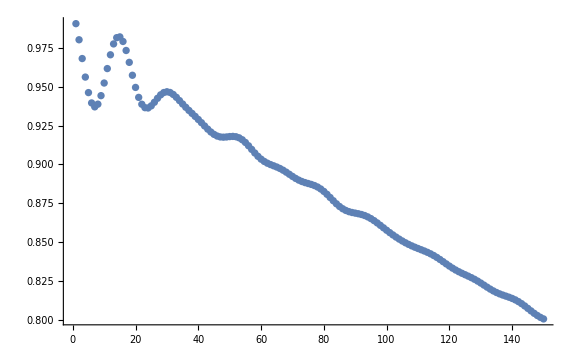

```mathematica
ListPlot[(szsz[5]-0sz[13+5]sz[13-5]),ImageSize->Large]
```

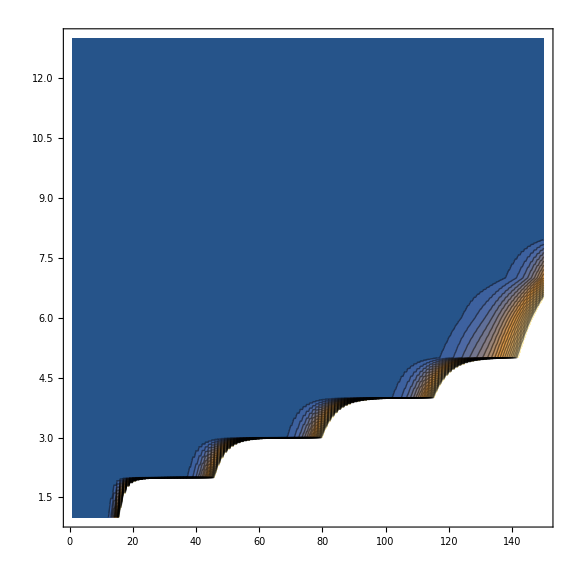

```mathematica
ListContourPlot[Table[(szsz[r]-sz[13+r]sz[13-r]),{r,1,13}],Contours->20,ImageSize->Large]
```

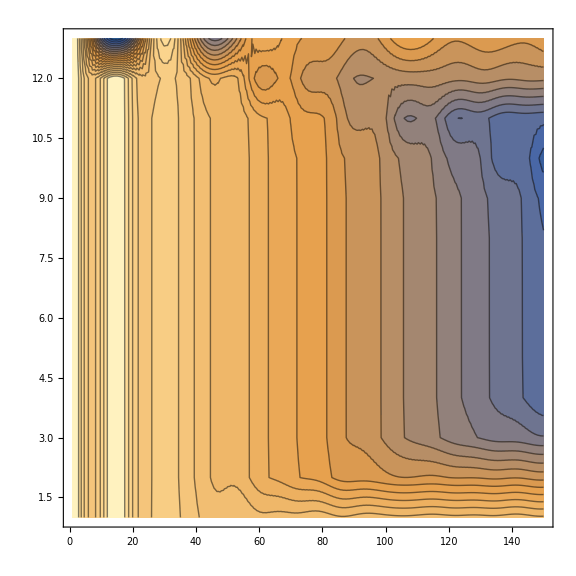

```mathematica
ListContourPlot[Table[(szsz[r]-0sz[13+r]sz[13-r]),{r,1,13}],Contours->20,ImageSize->Large]
```

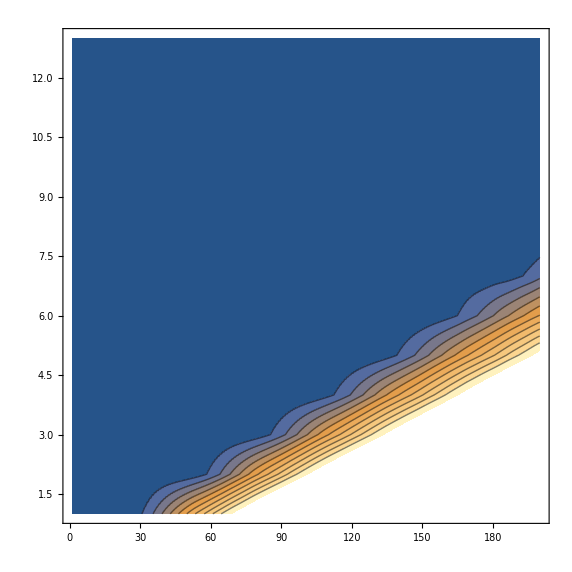

```mathematica
ListContourPlot[Table[(szsz[r]-sz[13+r]sz[13-r]),{r,1,13}],Contours->10]
```

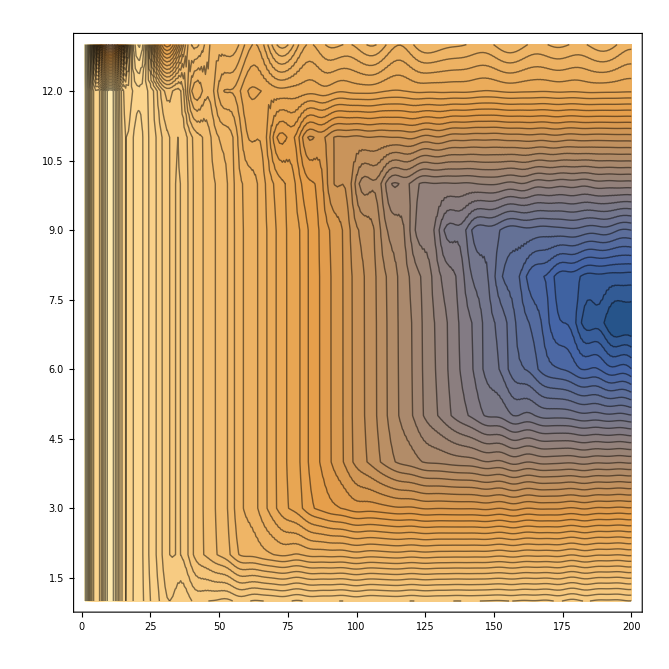

```mathematica
ListContourPlot[Table[(szsz[r]-sz[13+r]sz[13-r]),{r,1,13}],Contours->50]
```

```mathematica
1+26*2
```

53

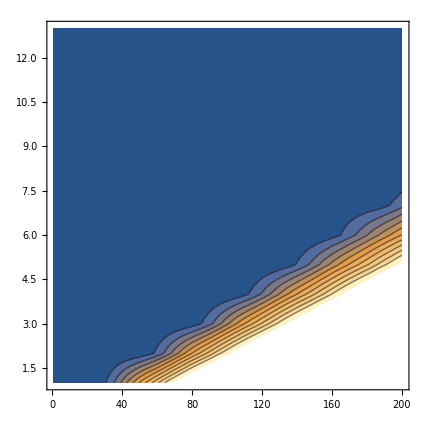
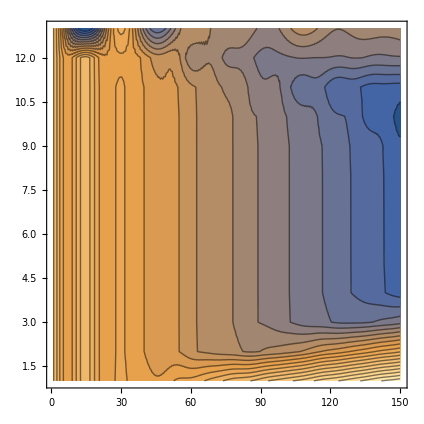
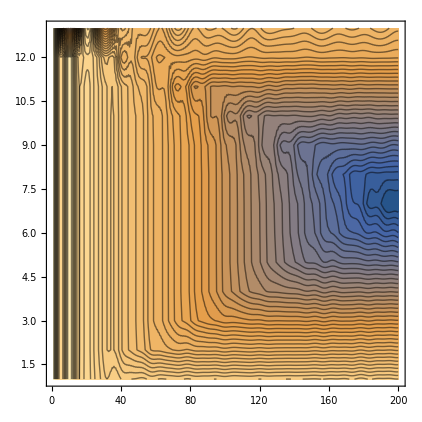

```mathematica
t = data[[All,1]];
energy = data[[All,2]];
mag = data[[All,3]];
```

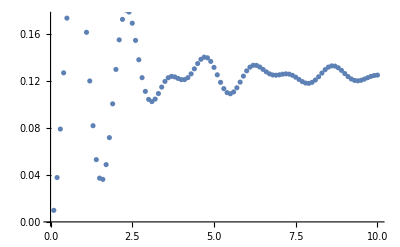

```mathematica
ListPlot[Thread[List[t,mag]]]
```

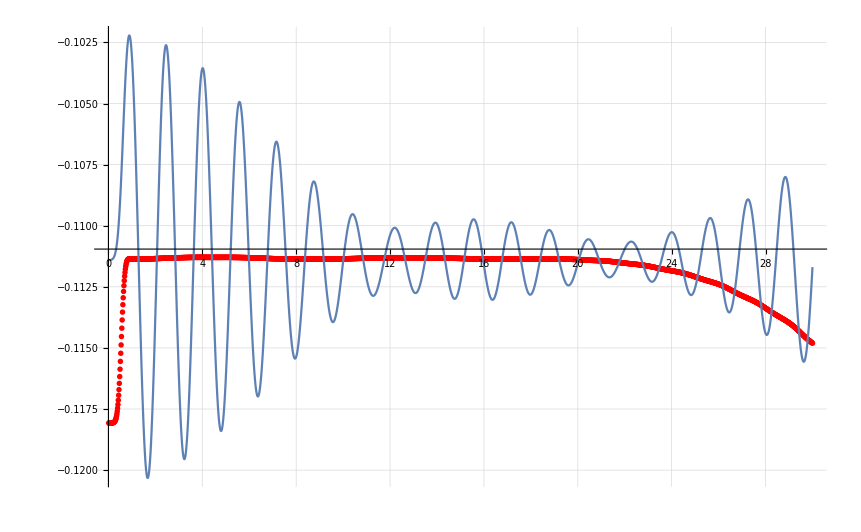

```mathematica
Show[ListPlot[Thread[List[t,((energy-energy[[1000]])+Mean[Drop[mag,1]])]],PlotStyle->Red,PlotRange->Full],ListPlot[Thread[List[t,mag]],Joined->True,PlotRange->Full],PlotRange->Automatic,GridLines->Automatic,ImageSize->Large]
```

```mathematica
ts = TimeSeries[Drop[Thread[{t,mag-Mean[mag[[200;;1500]]]}],1]]
```

TimeSeries[…]

```mathematica
PowerSpectralDensity[ts,ω]
```

8.37531×10^-6+2 (8.36085×10^-6 Cos[ω]+8.31759×10^-6 Cos[2 ω]+8.24569×10^-6 Cos[3 ω]+8.14543×10^-6 Cos[4 ω]+3008+9.86387×10^-11 Cos[1996 ω]+6.14986×10^-11 Cos[1997 ω]+3.25189×10^-11 Cos[1998 ω]+1.19613×10^-11 Cos[1999 ω])
 |  |  |  |

```mathematica
PowerSpectralDensity[ts,ω,HannWindow]
```

8.37531×10^-6+2 (0.+8.36085×10^-6 Cos[ω]+8.31757×10^-6 Cos[2 ω]+8.24564×10^-6 Cos[3 ω]+8.14535×10^-6 Cos[4 ω]+3007+1.41844×10^-15 Cos[1995 ω]+5.48155×10^-16 Cos[1996 ω]+1.51893×10^-16 Cos[1997 ω]+2.00794×10^-17 Cos[1998 ω])
 |  |  |  |

```mathematica
30/2000(0.06/(2Pi))^-1//N
```

1.5708

8.37531×10^-6+2 (0.+8.35667×10^-6 Cos[ω]+8.30925×10^-6 Cos[2 ω]+8.23328×10^-6 Cos[3 ω]+8.12906×10^-6 Cos[4 ω]+3007+5.2286×10^-16 Cos[1995 ω]+2.01958×10^-16 Cos[1996 ω]+5.59344×10^-17 Cos[1997 ω]+7.39048×10^-18 Cos[1998 ω])
 |  |  |  |

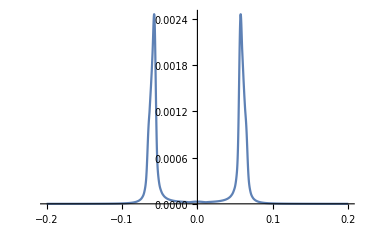

```mathematica
PowerSpectralDensity[ts,ω,HannPoissonWindow]
Plot[%,{ω,-0.2,0.2},PlotRange->Full]
```

```mathematica
FindMaximum[PowerSpectralDensity[ts,ω,HannPoissonWindow],{ω,0.07}]
```

{0.00246108,{ω→0.0573777}}

```mathematica
(t[[1500]]-t[[200]])/1300/(0.0573776546308995/(2Pi))
```

1.64259

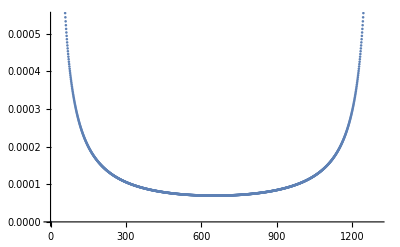

```mathematica
ListPlot[Fourier[Drop[mag[[200;;1500]],1]-Mean[Drop[mag[[200;;1500]],1]]]//Abs]
```

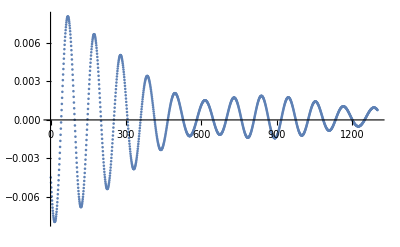

```mathematica
Drop[mag[[200;;1500]],1]-Mean[Drop[mag[[1500;;All]],1]]//ListPlot
```